# Symbolic Regression of Pendulum Data

## Introduction

## Lagrangians

### Euler Lagrange Equations

### Converting Expression from Cloure.

## Single Pendulum

### Theoretical Lagrangian

Theoretical single pendulum Lagrangian is of the form:

(L=1/2 mr^2(dθ/dt))^2-mgr(1-cosθ)

```mathematica
mass=1
length=1
gravity=1

simplepenlag[theta_,thetaprime_]:=(1/2*mass*length^2*thetaprime^2)-mass*gravity*length*(1-Cos[theta])
```

1

1

1

```mathematica
singpendata = Import["/Users/joelrussell/Documents/Imperial/Year_4/Masters_Project/Code/joel_flow/flow/data/mma_pendulum_large.csv"] //Short

theta={#⟦1⟧&/@singpendata} 
thetaprime={#⟦2⟧&/@singpendata}
```

(«1»)

{{2.98451,-2.71051×10^-20}}

{{2.98137,-0.0629866}}

```mathematica
ListPlot[theta,AxesLabel->θ]
ListPlot[thetaprime,AxesLabel->θ']
```

-Graphics-

-Graphics-

```mathematica
ListPlot[simplepenlag[theta,thetaprime],AxesLabel->lagrangian]
```

-Graphics-

### Numerical Lagrangian Expressions

```mathematica
triallag1[theta_,omega_]:=Times[Times[0.022210588271571317, Plus[Plus[Plus[Plus[Plus[Plus[Plus[Cos[omega], Cos[theta]], Times[Cos[theta], 0.6247552574671112]], Cos[theta]], Times[Plus[Plus[Plus[Plus[Cos[omega], Cos[theta]], Cos[theta]], Cos[theta]], Cos[theta]], Cos[theta]]], omega], omega], Cos[theta]]], Sin[theta]]
```

```mathematica
run1[theta_,omega_]:=Plus[Sin[theta], Plus[Times[Sin[theta], Cos[theta]], Times[Times[Sin[theta], 0.12642579887098596], Times[omega, omega]]]]
run2[theta_,omega_]:=Times[Plus[Plus[Sin[theta], Subtract[Plus[Sin[theta], 1.9273329585287498], Sin[theta]]], Plus[Times[Sin[theta], Cos[theta]], Times[Times[Sin[theta], 0.12641372676463694], Times[omega, omega]]]], 0.06703977631709543]

ListPlot[run1[theta,thetaprime]]
ListPlot[run2[theta,thetaprime]]
```

-Graphics-

-Graphics-

### Euler Lagrange Equations

```mathematica
Needs["VariationalMethods`"]
```

#### THEORETICAL

1

1

9.8

Theoretical Values with Algebraic Representations of m g and l

mgr (1-cos(θ(t)))+1/2 mr^2 (θ'(t))^2

mgr sin(θ(t))-mr^2 θ''(t)==0

{{θ''(t)→(mgr sin(θ(t)))/mr^2}}

1/2 (θ'(t))^2+9.8 (1-cos(θ(t)))

9.8 sin(θ(t))-θ''(t)==0

{9.8 sin(θ(t))-θ''(t)==0,θ(0)==2.98451,θ'(0)==-2.71051×10^-20}

{{θ(t)→InterpolatingFunction[{{0., 30.}}, <>](t)}}

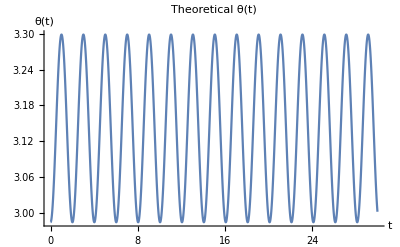

```mathematica
Clear[m,l,g]

m = 1
l = 1
g = 9.8

"Theoretical Values with Algebraic Representations of m g and l"

theorylag = 1/2 mr^2 θ'[t]^2+mgr(1-Cos[θ[t]])
theoryEL = EulerEquations[theorylag,θ[t],t]
theorysol = Solve[theoryEL,θ''[t]]

theorylagn = 1/2 m*l^2*θ'[t]^2+m*g*l*(1-Cos[θ[t]])

ELth = EulerEquations[theorylagn,θ[t],t]

s =Join[List[ELth],{θ[0] == 2.9845130209103,θ'[0] == -2.71050543121376*10^-20}]

theorysoln = NDSolve[s,θ[t],{t,0,30}]

Plot[Evaluate[θ[t]/.theorysoln],{t,0,30},PlotRange->All,PlotLabel->Theoretical θ[t],AxesLabel->{t,θ[t]}]
```

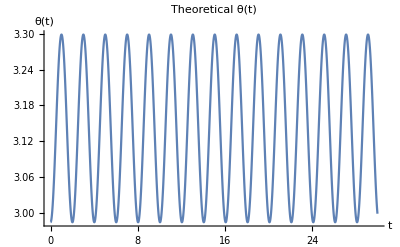

```mathematica
"theorylag[mass_,length_,gravity_] := 1/2mass*length^2*"
```

theorylag[mass_,length_,gravity_] := 1/2mass*length^2*

#### EXPERIMENTAL

0.0670398 (0.126401 omega^2 sin(theta)+sin(theta)+sin(theta) cos(theta))

0.0670398 (0.126401 sin(theta) (θ'(t))^2+sin(theta)+sin(theta) cos(theta))

0.0670398 (0.126401 (θ'(t))^2 sin(θ(t))+sin(θ(t))+sin(θ(t)) cos(θ(t)))

-0.0169478 θ''(t) sin(θ(t))-0.00847391 (θ'(t))^2 cos(θ(t))-0.0670398 sin^2(θ(t))+0.0670398 cos^2(θ(t))+0.0670398 cos(θ(t))==0

{-0.0169478 θ''(t) sin(θ(t))-0.00847391 (θ'(t))^2 cos(θ(t))-0.0670398 sin^2(θ(t))+0.0670398 cos^2(θ(t))+0.0670398 cos(θ(t))==0,θ(0)==2.98451,θ'(0)==-2.71051×10^-20}

{{θ(t)→InterpolatingFunction[{{0., 30.}}, <>](t)}}

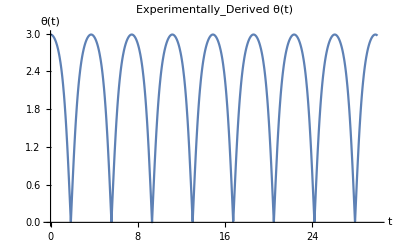

```mathematica
Clear[theta]

L= Times[Plus[Sin[theta], Plus[Times[Sin[theta], Cos[theta]], Times[Times[Sin[theta], 0.1264012221818857], Times[omega, omega]]]], 0.06703977631709543]

L = L/.omega->θ'[t]
L = L/.theta->θ[t]

ELexp = EulerEquations[L,θ[t],t]

Clear[s]

s =Join[List[ELexp],{θ[0] == 2.9845130209103,θ'[0] == -2.71050543121376*10^-20}]

expsoln = NDSolve[s,θ[t],{t,0,30}]

Plot[Evaluate[θ[t]/.expsoln],{t,0,30},PlotRange->All,PlotLabel->Experimentally_Derived θ[t],AxesLabel->{t,θ[t]}]
```

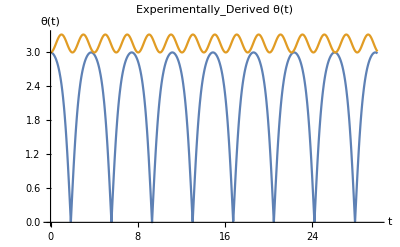

```mathematica
Plot[{Evaluate[θ[t]/.expsoln], Evaluate[θ[t]/.theorysoln]},{t,0,30},PlotRange->All,PlotLabel->Experimentally_Derived θ[t],AxesLabel->{t,θ[t]}]
```

## Double Pendulum

### Theoretical Lagrangian

Theoretical double pendulum lagrangian is of the form:

L = 1/2 (m_1+m_2)(l_1^2(dθ_1/dt))^2+1/2 m_2(l_2^2(dθ_2/dt))^2+m_2 l_1 l_2(dθ_1/dt)(dθ_2/dt)cos(θ_1-θ_2)+(m_1+m_2)gl_1 cos(θ_1)+m_2 gl_2 cos(θ_2)

```mathematica
"Parameters:"
Subscript[m, 1] = 1 
Subscript[l, 1] = 1
Subscript[m, 2] = 1
Subscript[l, 2] = 1
g = 9.8

Clear[theorylag]
Clear[theoryEL]
Clear[theorysol]

theorylag = 1/2*(m1+m2)*l1^2*(Subscript[θ, 1]'[t])^2+1/2*m2*l2^2*(Subscript[θ, 2]'[t])^2+m2*l1*l2*(Subscript[θ, 1]'[t])*(Subscript[θ, 2]'[t])*cos(Subscript[θ, 1][t]-Subscript[θ, 2][t])+m1*gr*l1*(cos(Subscript[θ, 1][t]))+m2*gr*l1*(cos(Subscript[θ, 1][t]))+m2*gr*l2*cos(Subscript[θ, 2][t])
theoryEL = EulerEquations[theorylag,{Subscript[θ, 1][t],Subscript[θ, 2][t]},t]
"theorysol"
theorysol = Solve[theoryEL,{Subscript[θ, 1]''[t],Subscript[θ, 2]''[t]}]

Clear[theorylagn]
Clear[ELth]
Clear[s]
Clear[theorysoln]

"Taking values for constants"
theorylagn = 1/2(Subscript[m, 1]+Subscript[m, 2])Subscript[l, 1]^2*(Subscript[θ, 1]'[t])^2+1/2 Subscript[m, 2]*Subscript[l, 2]^2*(Subscript[θ, 2]'[t])^2+Subscript[m, 2]*Subscript[l, 1]*Subscript[l, 2]*(Subscript[θ, 1]'[t])*(Subscript[θ, 2]'[t])cos(Subscript[θ, 1][t]-Subscript[θ, 2][t])+(Subscript[m, 1]+Subscript[m, 2])g*Subscript[l, 1]*cos(Subscript[θ, 1][t])+Subscript[m, 2]*g*Subscript[l, 2]*cos(Subscript[θ, 2][t])
"Euler equations"
ELth = EulerEquations[theorylagn,{Subscript[θ, 1][t],Subscript[θ, 2][t]},t]

List[Part[ELth,1]]

s1 =Join[List[Part[ELth,1]],{Subscript[θ, 1][0] == 2.9845130209103,Subscript[θ, 1]'[0] == -2.71050543121376*10^-20,Subscript[θ, 2][0] == 2.9845130209103,Subscript[θ, 2]'[0] == -2.71050543121376*10^-20}]
s2 =Join[List[Part[ELth,2]],{Subscript[θ, 2][0] == 2.9845130209103,Subscript[θ, 2]'[0] == -2.71050543121376*10^-20}]

theorysoln1 = NDSolve[s1,Subscript[θ, 1][t],{t,0,30}]
theorysoln2 = NDSolve[s2,Subscript[θ, 2][t],{t,0,30}]


Plot[Evaluate[θ[t]/.theorysoln],{t,0,30},PlotRange->All,PlotLabel->Theoretical θ[t],AxesLabel->{t,θ[t]}]
```

Parameters:

1

1

1

«1 more identical outputs»

9.8

gr l1 m1 cos θ_1(t)+gr l1 m2 cos θ_1(t)+gr l2 m2 cos θ_2(t)+1/2 l1^2 (m1+m2) (θ_1'(t))^2+l1 l2 m2 cos (θ_1(t)-θ_2(t)) θ_2'(t) θ_1'(t)+1/2 l2^2 m2 (θ_2'(t))^2

{l1 (cos (gr (m1+m2)-l2 m2 θ_1(t) θ_2''(t)+l2 m2 θ_2(t) θ_2''(t))-l1 (m1+m2) θ_1''(t)+l2 m2 cos (θ_2'(t))^2)==0,-l2 m2 (-gr cos+l1 cos (θ_1'(t))^2+l1 cos θ_1(t) θ_1''(t)-l1 cos θ_2(t) θ_1''(t)+l2 θ_2''(t))==0}

theorysol

{{θ_1''(t)→-((l2^2 (-m2) (gr l1 cos (m1+m2)+l1 l2 m2 cos (θ_2'(t))^2)-(l1 l2 m2 cos θ_2(t)-l1 l2 m2 cos θ_1(t)) (gr l2 m2 cos-l1 l2 m2 cos (θ_1'(t))^2))/(l1^2 l2^2 m2 (m1+m2)-(l1 l2 m2 cos θ_2(t)-l1 l2 m2 cos θ_1(t))^2)),θ_2''(t)→-((-gr m1 cos^2 θ_1(t)+gr m1 cos^2 θ_2(t)+gr m1 cos-gr m2 cos^2 θ_1(t)+gr m2 cos^2 θ_2(t)+gr m2 cos-l1 m1 cos (θ_1'(t))^2-l1 m2 cos (θ_1'(t))^2-l2 m2 cos^2 θ_1(t) (θ_2'(t))^2+l2 m2 cos^2 θ_2(t) (θ_2'(t))^2)/(l2 (-m1+m2 cos^2 (θ_1(t))^2+m2 cos^2 (θ_2(t))^2-2 m2 cos^2 θ_1(t) θ_2(t)-m2)))}}

Taking values for constants

(θ_1'(t))^2+1/2 (θ_2'(t))^2+cos (θ_1(t)-θ_2(t)) θ_2'(t) θ_1'(t)+19.6 cos θ_1(t)+9.8 cos θ_2(t)

Euler equations

{cos (θ_2'(t))^2-2. θ_1''(t)+cos (-1. θ_1(t) θ_2''(t)+θ_2(t) θ_2''(t)+19.6)==0,-1. cos (θ_1'(t))^2-1. θ_2''(t)-1. cos θ_1(t) θ_1''(t)+cos θ_2(t) θ_1''(t)+9.8 cos==0}

{cos (θ_2'(t))^2-2. θ_1''(t)+cos (-1. θ_1(t) θ_2''(t)+θ_2(t) θ_2''(t)+19.6)==0}

{cos (θ_2'(t))^2-2. θ_1''(t)+cos (-1. θ_1(t) θ_2''(t)+θ_2(t) θ_2''(t)+19.6)==0,θ_1(0)==2.98451,θ_1'(0)==-2.71051×10^-20,θ_2(0)==2.98451,θ_2'(0)==-2.71051×10^-20}

{-1. cos (θ_1'(t))^2-1. θ_2''(t)-1. cos θ_1(t) θ_1''(t)+cos θ_2(t) θ_1''(t)+9.8 cos==0,θ_2(0)==2.98451,θ_2'(0)==-2.71051×10^-20}

NDSolve::underdet: There are more dependent variables, {θ_1(t),θ_2(t)}, than equations, so the system is underdetermined.

NDSolve[{cos (θ_2'(t))^2-2. θ_1''(t)+cos (-1. θ_1(t) θ_2''(t)+θ_2(t) θ_2''(t)+19.6)==0,θ_1(0)==2.98451,θ_1'(0)==-2.71051×10^-20,θ_2(0)==2.98451,θ_2'(0)==-2.71051×10^-20},θ_1(t),{t,0,30}]

NDSolve::underdet: There are more dependent variables, {θ_1(t),θ_2(t)}, than equations, so the system is underdetermined.

NDSolve[{-1. cos (θ_1'(t))^2-1. θ_2''(t)-1. cos θ_1(t) θ_1''(t)+cos θ_2(t) θ_1''(t)+9.8 cos==0,θ_2(0)==2.98451,θ_2'(0)==-2.71051×10^-20},θ_2(t),{t,0,30}]

ReplaceAll::reps: {theorysoln} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

Parameters:

1

1

1

«1 more identical outputs»

9.8

(θ_1'(t))^2

### Euler-Lagrange Equations

#### Theoretical

```mathematica
Simplify[Times[Times[Times[Times[Times[theta2, theta2], Times[Times[theta2, theta2], Times[Times[Times[theta2, theta2], Times[theta1, theta1]], Times[Times[Cos[omega1], Times[theta1, theta1]], Times[theta1, theta1]]]]], Times[theta1, theta1]], Times[Times[Times[theta2, theta2], Subtract[Sin[theta1], theta1]], Cos[omega2]]], Times[Times[theta2, theta2], Times[Times[theta2, theta2], Times[theta1, theta1]]]]]
Simplify[Times[Plus[Plus[Sin[theta2], Times[theta2, theta2]], Times[theta2, Cos[theta2]]], Times[Plus[Times[theta1, theta1], Times[theta1, theta1]], Subtract[Times[omega2, omega2], Times[omega1, omega1]]]]]
```

theta1^10 theta2^12 cos(omega1) cos(omega2) (sin(theta1)-theta1)

2 theta1^2 (omega2^2-omega1^2) (theta2^2+sin(theta2)+theta2 cos(theta2))

## Get some nuts

```mathematica
alex = {1.0, 1.0, 1.0, 1.0, 1.0, 1.0, 1.0, 1.0, 1.0, 1.0, 1.0, 1.0, 0.39405115348944997, 1.0, 1.0, 1.0, 0.322760970525832, 0.360931232190295, 0.3279677784207626, 0.3518985130905625, 1.0, 1.0, 1.0, 0.307887487520192, 1.0, 0.3521556101211658, 1.0, 0.40512806801574414, 0.41906765720200384, 1.0, 0.6413104691281454, 1.0, 0.618631820048457, 1.0, 1.0, 1.0, 1.0, 1.0, 1.0, 1.0, 1.0, 0.8646932479913982, 1.0, 1.0, 0.8526695881316044, 0.9093342591099541, 0.8594909692861791, 0.8243365497105928, 1.0}
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.394051,1.,1.,1.,0.322761,0.360931,0.327968,0.351899,1.,1.,1.,0.307887,1.,0.352156,1.,0.405128,0.419068,1.,0.64131,1.,0.618632,1.,1.,1.,1.,1.,1.,1.,1.,0.864693,1.,1.,0.85267,0.909334,0.859491,0.824337,1.}

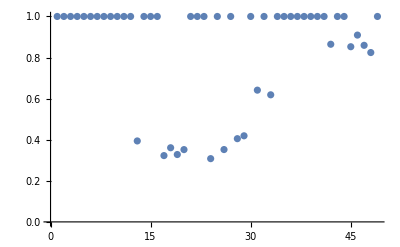

Syntax::sntxf: "alex=" cannot be followed by "[«1»]".

```mathematica
ListPlot[alex]
```